```mathematica
(* Directory for data *)
SetDirectory["\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2020\\11\\19\\continuous QE estimation 1"]
(* Filenames *)
fn=FileNames[];
```

\\fed.cclrc.ac.uk\Org\NLab\ASTeC\Projects\VELA\Work\2020\11\19\continuous QE estimation 1

```mathematica
(* load all tagged date and put in a assoc *)
alldat=Association[Prepend[{{"fn"->#},{"date"->DateObject[ToExpression@StringSplit[StringDrop[#,-5],"_"]⟦2;;-1⟧]}},Import[#]]]&/@fn⟦1;;-1⟧;
```

```mathematica
(* tags in this data set *)
Transpose[{Range@Length@Normal[alldat⟦1⟧],Normal[alldat⟦1⟧]⟦All,1⟧}]//TableForm
```

1 | KLYSTRON_FORWARD_POWER
2 | LRRG_CAVITY_FORWARD_POWER
3 | gun_rf_phase_FF
4 | gun_rf_phase_SP
5 | gun_rf_phase_lock
6 | Q_pv
7 | E_pv
8 | bsol_seti_pv
9 | bsol_pow_pv
10 | sol2_seti_pv
11 | sol2_pow_pv
12 | las_sigma_x
13 | las_sigma_y
14 | las_x
15 | las_y
16 | las_cam_avg_int
17 | fn
18 | date

```mathematica
(* make some cuts to remove 0 Laser energy, low Q, and after a times *)
cut1=Select[alldat,Lookup[#,"las_cam_avg_int"]>110&];
cut2=Select[cut1,Lookup[#,"E_pv"]>0&];
cut2=Select[cut2,Lookup[#,"Q_pv"]>5&];
cut4=Select[cut3,Lookup[#,"date"]>DateObject[{2020,11,18,16,0,0}]&];
Length/@{cut1,cut2,cut3,cut4}
```

{371,263,239,239}

```mathematica
tags={"gun_rf_phase_FF","gun_rf_phase_SP","gun_rf_phase_lock","bsol_seti_pv","bsol_pow_pv","sol2_seti_pv","sol2_pow_pv","las_sigma_x","las_sigma_y","las_x","las_y","las_cam_avg_int"}
```

{gun_rf_phase_FF,gun_rf_phase_SP,gun_rf_phase_lock,bsol_seti_pv,bsol_pow_pv,sol2_seti_pv,sol2_pow_pv,las_sigma_x,las_sigma_y,las_x,las_y,las_cam_avg_int}

```mathematica
normPLot[data_,ylabel_,label_]:=Block[{},DateListPlot[Transpose[{data⟦All,1⟧,data⟦All,2⟧/RandomChoice[data⟦All,2⟧]}],BaseStyle->{FontSize->18},Joined->False,FrameLabel->{"Time",ylabel<>" (AU)"},PlotLabel->label,ImageSize->500]]
dataPLot[data_,ylabel_,label_]:=Block[{},DateListPlot[Transpose[{data⟦All,1⟧,data⟦All,2⟧}],BaseStyle->{FontSize->18},Joined->False,FrameLabel->{"Time",ylabel},PlotLabel->label,ImageSize->500]]
```

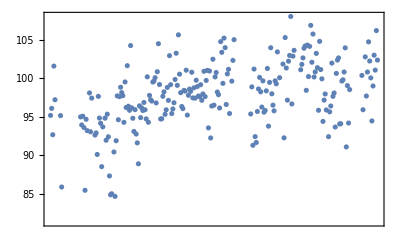

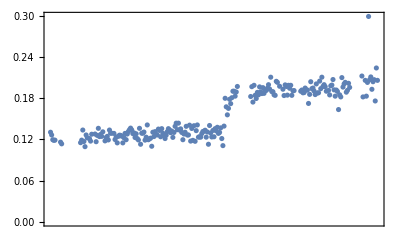

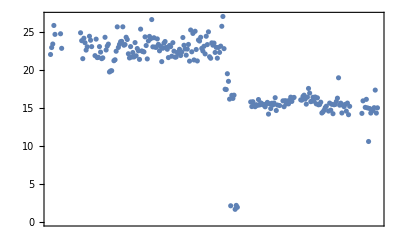

```mathematica
(* DO some plots *)
DateListPlot[Transpose[{Lookup[cut4,"date"],Lookup[cut4,"Q_pv"]}],Joined->False]
DateListPlot[Transpose[{Lookup[cut4,"date"],Lookup[cut4,"E_pv"]}],Joined->False]
(* *)
c1=4.66 10^-6;
c2=15.4;
DateListPlot[Transpose[{Lookup[cut4,"date"],c1/c2 Lookup[cut4,"Q_pv"]/Lookup[cut4,"E_pv"] 10^5}],Joined->False]
```

```mathematica
dataPLot[Transpose[{Lookup[cut4,"date"],Lookup[cut4,"Q_pv"]}],"Q ","KLYSTRON_FORWARD_POWER"]
```

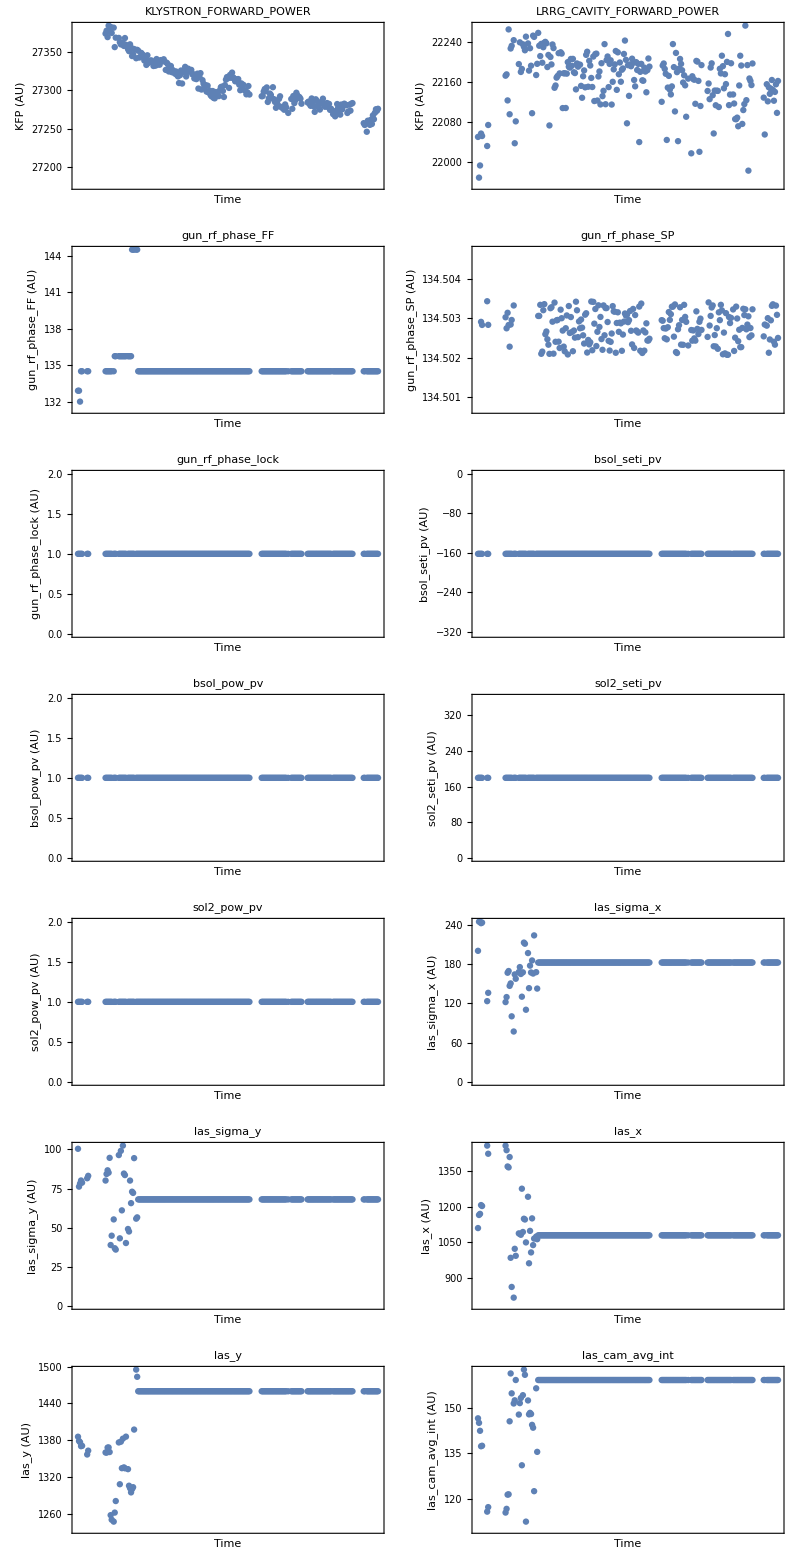

```mathematica
TableForm[Partition[Join[{dataPLot[Transpose[{Lookup[cut4,"date"],Mean[#⟦360;;380⟧]&/@Lookup[cut4,"KLYSTRON_FORWARD_POWER"]}],"KFP ","KLYSTRON_FORWARD_POWER"],
dataPLot[Transpose[{Lookup[cut4,"date"],Mean[#⟦360;;380⟧]&/@Lookup[cut4,"LRRG_CAVITY_FORWARD_POWER"]}],"KFP ","LRRG_CAVITY_FORWARD_POWER"]},dataPLot[Transpose[{Lookup[cut4,"date"],Lookup[cut4,#]}],#<>" ",#]&/@tags],2]]
```

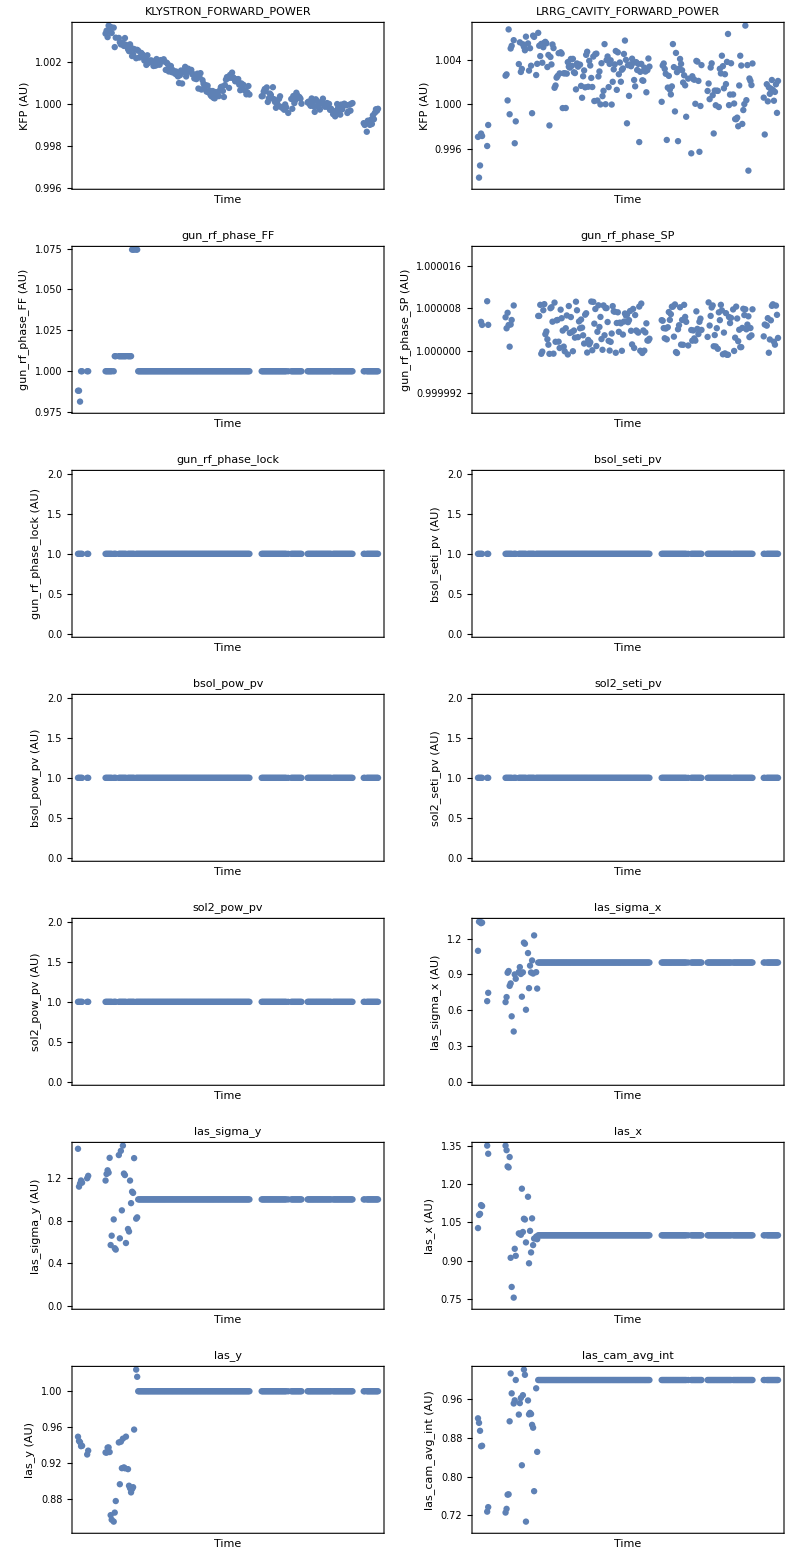

```mathematica
TableForm[Partition[Join[{normaPLot[Transpose[{Lookup[cut4,"date"],Mean[#⟦360;;380⟧]&/@Lookup[cut4,"KLYSTRON_FORWARD_POWER"]}],"KFP ","KLYSTRON_FORWARD_POWER"],
normaPLot[Transpose[{Lookup[cut4,"date"],Mean[#⟦360;;380⟧]&/@Lookup[cut4,"LRRG_CAVITY_FORWARD_POWER"]}],"KFP ","LRRG_CAVITY_FORWARD_POWER"]},normaPLot[Transpose[{Lookup[cut4,"date"],Lookup[cut4,#]}],#<>" ",#]&/@tags],2]]
```